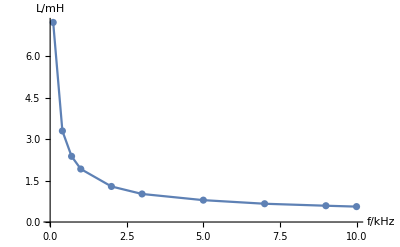

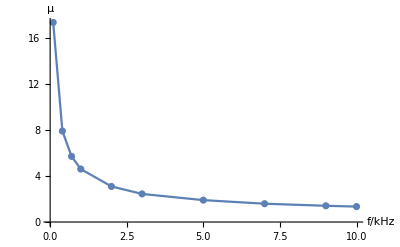

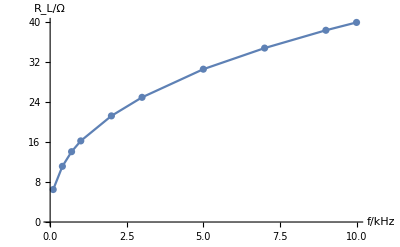

```mathematica
f={0.1,0.4,0.7,1,2,3,5,7,9,10};
L={7.23,3.30,2.38,1.92,1.288,1.016,0.792,0.662,0.590,0.558};
Mu={17.33,7.90,5.70,4.60,3.09,2.44,1.90,1.59,1.41,1.34};
RL={6.509,11.159,14.097,16.257,21.27,24.99,30.63,34.86,38.43,40.00};
data1=Table[{f[[i]],L[[i]]},{i,1,10}];
data2=Table[{f[[i]],Mu[[i]]},{i,1,10}];
data3=Table[{f[[i]],RL[[i]]},{i,1,10}];
pd1=ListPlot[data1];
pd1l=ListLinePlot[data1];
pd2=ListPlot[data2];
pd2l=ListLinePlot[data2];
pd3=ListPlot[data3];
pd3l=ListLinePlot[data3];
Show[pd1,pd1l,AxesLabel->{HoldForm[f/kHz],HoldForm[L/mH]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
Show[pd2,pd2l,AxesLabel->{HoldForm[f/kHz],HoldForm[μ]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
Show[pd3,pd3l,AxesLabel->{HoldForm[f/kHz],HoldForm[R_L/Ω]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```